```mathematica
AppendTo[$Path,"C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\GeneralTile"];
Get["HappyCluster.wl"]
Get["HappyTile.wl"]
```

## Graph Function

```mathematica
leaves=Function[g,Select[VertexList[g],VertexOutDegree[g,#]==0&]];
```

```mathematica
depthNode[n_]:=Function[g,With[{root=First[VertexList[g]]},Select[VertexList[g],GraphDistance[g,root,#]==n&]]]
```

## Compare with hat tiling

```mathematica
compare[code_]:=Block[{graph,reBuiltCodes},
graph=tilingTopologicalGraph[<|False->h7Tile,True->h8Tile|>][{(clusterVertices@@#)[[4]],#[[2]],1,#[[4]]}&/@code];
reBuiltCodes=buildClusterCodes[h2Tile,h1Tile][graph];
{
Show[#,Graphics[{Red,Disk[{0,0},.7]}]]&@visualize[code],
Graphics[{Lighter@Blue,Opacity[.5],EdgeForm[Black],(metaTile[#1,#2,2,#4]&@@@
Select[reBuiltCodes,FreeQ[Missing]])}]
}
];
```

## Previous Result

```mathematica
oneThirdTheoremListCluster=;
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

## Eliminate super{12,12,12}

```mathematica
super12=Prepend[#,{0,0}]&/@oneThirdTheoremListCluster[[-3]];
```

```mathematica
g=NestGraph[growH8Tiling[#,branchNumLimit->Infinity]&,clusterTilingState[super12],3];
```

impossible Vertices:{{18,4 √3},{14,4 √3},{12,4 √3},{16,4 √3},{16,2 √3},{18,2 √3},{14,2 √3},{-15,7 √3},{-13,5 √3},{-12,4 √3},{-14,6 √3},{-11,7 √3},{-12,8 √3},{-10,6 √3},{-3,-11 √3},{-1,-9 √3},{0,-8 √3},{-2,-10 √3},{-5,-9 √3},{-6,-10 √3},{-4,-8 √3}}

```mathematica
drawClusterInfomration/@VertexList[g]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Delete[oneThirdTheoremListCluster,{-3}]//Iconize
```

```mathematica
oneThirdTheoremListCluster=;
```

## See something from pre-image

```mathematica
Get["toptile.wl"]
```

```mathematica
inits=Map[Prepend[#,{0,0}]&,oneThirdAndTwoThirdTheoremListCluster,{2}];
```

```mathematica
maybeInvalid={1,3,7,11,14,18,21,24,30,36,37,38,44,55,58,63};
```

Grow once and draw their pre-image to see if it is a candidate invalid.

### Maps

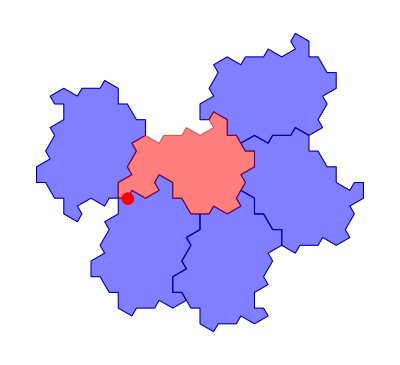
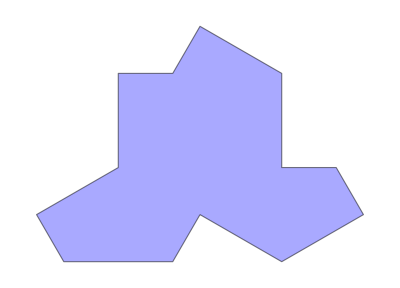
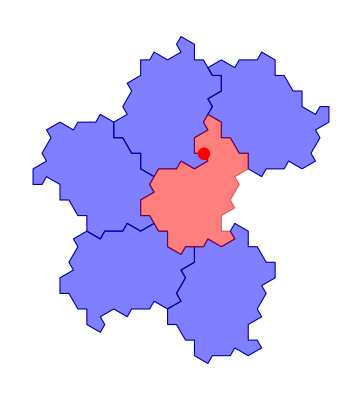
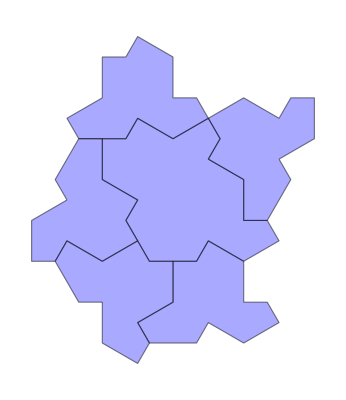
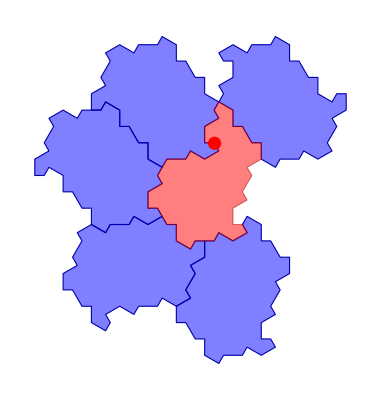
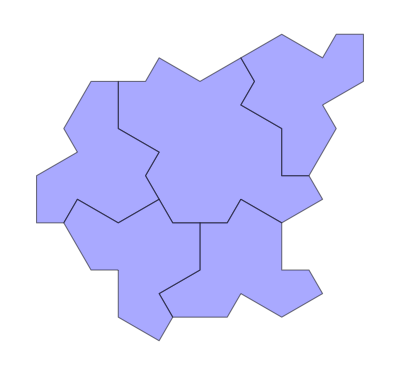
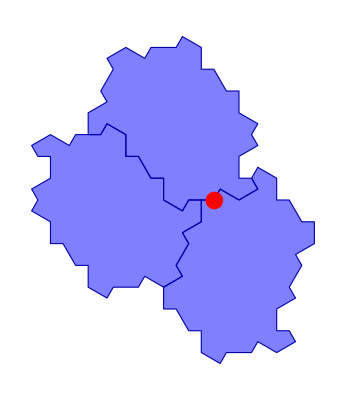
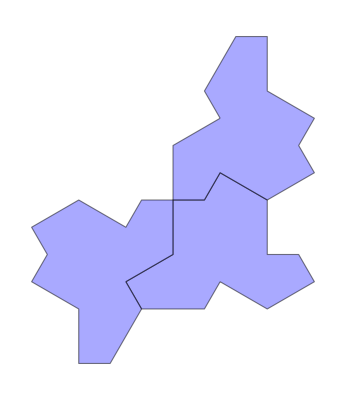
-Graphics-↔-Graphics-1 | -Graphics-↔-Graphics-2 | -Graphics-↔-Graphics-3
-Graphics-↔-Graphics--Graphics-↔-Graphics-4 | -Graphics-↔-Graphics-5 | -Graphics-↔-Graphics--Graphics-↔-Graphics-6
-Graphics-↔-Graphics-7 | -Graphics-↔-Graphics-8 | -Graphics-↔-Graphics-9
-Graphics-↔-Graphics-10 | -Graphics-↔-Graphics-11 | -Graphics-↔-Graphics-12
-Graphics-↔-Graphics--Graphics-↔-Graphics--Graphics-↔-Graphics-13 | -Graphics-↔-Graphics-14 | -Graphics-↔-Graphics-15
-Graphics-↔-Graphics-16 | -Graphics-↔-Graphics-17 | -Graphics-↔-Graphics-18
-Graphics-↔-Graphics-19 | -Graphics-↔-Graphics--Graphics-↔-Graphics-20 | -Graphics-↔-Graphics-21
-Graphics-↔-Graphics-22 | -Graphics-↔-Graphics-23 | -Graphics-↔-Graphics-24
-Graphics-↔-Graphics-25 | -Graphics-↔-Graphics-26 | -Graphics-↔-Graphics--Graphics-↔-Graphics-27
-Graphics-↔-Graphics-28 | -Graphics-↔-Graphics--Graphics-↔-Graphics-29 | -Graphics-↔-Graphics-30
-Graphics-↔-Graphics-31 | -Graphics-↔-Graphics-32 | -Graphics-↔-Graphics-33
-Graphics-↔-Graphics-34 | -Graphics-↔-Graphics-35 | -Graphics-↔-Graphics-36
-Graphics-↔-Graphics-37 | -Graphics-↔-Graphics-38 | -Graphics-↔-Graphics-39
-Graphics-↔-Graphics-40 | -Graphics-↔-Graphics-41 | -Graphics-↔-Graphics-42
-Graphics-↔-Graphics-43 | -Graphics-↔-Graphics-44 | -Graphics-↔-Graphics-45
-Graphics-↔-Graphics-46 | -Graphics-↔-Graphics-47 | -Graphics-↔-Graphics-48
-Graphics-↔-Graphics--Graphics-↔-Graphics--Graphics-↔-Graphics-49 | -Graphics-↔-Graphics-50 | -Graphics-↔-Graphics--Graphics-↔-Graphics-51
-Graphics-↔-Graphics--Graphics-↔-Graphics--Graphics-↔-Graphics-52 | -Graphics-↔-Graphics-53 | -Graphics-↔-Graphics--Graphics-↔-Graphics-54
-Graphics-↔-Graphics-55 | -Graphics-↔-Graphics-56 | -Graphics-↔-Graphics-57
-Graphics-↔-Graphics-58 | -Graphics-↔-Graphics-59 | -Graphics-↔-Graphics-60
-Graphics-↔-Graphics-61 | -Graphics-↔-Graphics--Graphics-↔-Graphics--Graphics-↔-Graphics-62 | -Graphics-↔-Graphics-63
-Graphics-↔-Graphics-64 | -Graphics-↔-Graphics-65 | -Graphics-↔-Graphics-66

```mathematica
MapIndexed[
Labeled[
Row@Function[code,
Block[{graph,reBuiltCodes,res=growH8Tiling[clusterTilingState[code],branchNumLimit->Infinity]},
graph=tilingTopologicalGraph[<|False->h7Tile,True->h8Tile|>][{(clusterVertices@@#)[[4]],#[[2]],1,#[[4]]}&/@#["code"]]&/@res;
reBuiltCodes=buildClusterCodes[h2Tile,h1Tile]/@graph;
MapThread[
Row[{
Show[#,Graphics[{Red,Disk[{0,0},.7]}]]&@visualize[#1["code"],ChooseColor->{Blue,Red}],
Graphics[{Lighter@Blue,Opacity[.5],EdgeForm[Black],(metaTile[#1,#2,2,#4]&@@@
Select[#2,FreeQ[Missing]])}]
},Style["↔",40,Gray]
]&,{res,reBuiltCodes}
]]][#1],
First[#2]
]&,inits]//Partition[#,UpTo[3]]&//Grid
```

## Eliminate more

```mathematica
maybeInvalidCodes=Map[Prepend[#,{0,0}]&,oneThirdAndTwoThirdTheoremListCluster[[maybeInvalid]],{2}];
```

```mathematica
groups=ReverseSortBy[Length]@GroupBy[maybeInvalidCodes,{Norm[Subtract@@(First@*clusterVertices@@@#)],Norm[Subtract@@(Last@*clusterVertices@@@#)],Sort[#[[All,4]]]}&];
```

They have 4 groups of v.f. actually. So we only need to eliminate 2 cases.

```mathematica
Map[Show[visualize[#],ImageSize->100]&,Values[groups],{2}]//Grid
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- |  |

### Eliminate Group 1 (5 cases)

```mathematica
g=Reap[NestGraph[growH8Tiling[#,branchNumLimit->Infinity]&,clusterTilingState[#],2]]&/@groups[[1]];//Timing
```

impossible Vertices:{{-4,0}}

impossible Vertices:{{2,4 √3}}

impossible Vertices:{{5,5 √3}}

impossible Vertices:{{3,5 √3}}

impossible Vertices:{{-11,√3}}

{14.9531,Null}

```mathematica
Show[visualize[Last[VertexList[#[[1]]]]["code"]],Graphics[{Red,Disk[#[[2,1,1]],.8]}]]&/@g//GraphicsRow[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
DeleteCases[oneThirdAndTwoThirdTheoremListCluster,Alternatives@@groups[[1]][[All,All,2;;]]]//Iconize
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

### Eliminate Group 2 (5 cases)

```mathematica
g2=Reap[NestGraph[growH8Tiling[#,branchNumLimit->Infinity]&,clusterTilingState[#],2]]&/@groups[[2]];//Timing
```

impossible Vertices:{{-1,√3}}

impossible Vertices:{{2,4 √3}}

impossible Vertices:{{1,5 √3}}

impossible Vertices:{{1,3 √3}}

impossible Vertices:{{0,2 √3}}

{5.03125,Null}

```mathematica
MapThread[Show[visualize[#1],Graphics[{Red,Disk[#2[[2,1,1]],.8]}]]&,{groups[[2]],g2}]//GraphicsRow[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
DeleteCases[oneThirdAndTwoThirdTheoremListCluster,Alternatives@@(groups[[2]][[All,All,2;;]])]//Iconize
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

### Eliminate Group 3 (3 cases)

```mathematica
g3=Reap[NestGraph[growH8Tiling[#,branchNumLimit->Infinity]&,clusterTilingState[#],2]]&/@groups[[3]];//Timing
```

impossible Vertices:{{-4,0},{-2,0}}

impossible Vertices:{{-6,0},{-4,0}}

impossible Vertices:{{-5,3 √3},{-4,2 √3}}

{3.15625,Null}

```mathematica
MapThread[Show[visualize[#1],Graphics[{Red,Disk[#2[[2,1,1]],.8]}]]&,{groups[[3]],g3}]//GraphicsRow[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-

```mathematica
DeleteCases[oneThirdAndTwoThirdTheoremListCluster,Alternatives@@(groups[[3]][[All,All,2;;]])]//Iconize
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

### Eliminate Group 4 (3 cases)

For time saving, we only choose one case to eliminate. They are the same.

```mathematica
g4=Reap[NestGraph[growH8Tiling[#,branchNumLimit->Infinity]&,clusterTilingState[#],60]]&@groups[[4,1]];//Timing
```

invalid Vertices:{{-9,5 √3}}

invalid Vertices:{{12,-2 √3}}

impossible Vertices:{{-44,6 √3},{-42,6 √3},{-40,4 √3},{-39,3 √3},{-41,5 √3},{-38,0},{-39,√3},{-37,-√3},{-42,0},{-41,-√3},{-40,2 √3},{-39,-√3},{-38,-2 √3}}

impossible Vertices:{{47,-3 √3},{45,-3 √3},{43,-√3},{42,0},{44,-2 √3},{41,3 √3},{42,2 √3},{40,4 √3},{45,3 √3},{44,4 √3},{43,√3},{42,4 √3},{41,5 √3}}

impossible Vertices:{{-24,-4 √3},{-25,-5 √3},{-25,-3 √3},{-27,-√3},{-26,-2 √3},{-29,-3 √3},{-30,-2 √3},{-27,-5 √3},{-28,-4 √3}}

impossible Vertices:{{-36,-2 √3},{-34,-2 √3}}

impossible Vertices:{{-52,-28 √3},{-54,-28 √3},{-50,-28 √3},{-54,-30 √3},{-52,-30 √3},{-51,-29 √3},{-49,-29 √3}}

{638.313,Null}

```mathematica
Iconize[g4[[1]]]
```

```mathematica
SelectFirst[Range[100,1,-1],Length[depthNode[#][g4[[1]]]]!=0&]
```

54

```mathematica
Graph[g4[[1]],GraphLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

```mathematica
drawClusterInfomration/@leaves[g4[[1]]]//Partition[#,UpTo[7]]&//Grid
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Same result as before.

```mathematica
DeleteCases[oneThirdAndTwoThirdTheoremListCluster,Alternatives@@groups[[4]][[All,All,2;;]]]//Iconize
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

### Eliminate super-{6,6,6}

Now the super-{6,6,6} is forced into dead end, as normal {6,6,6} does.

```mathematica
superSymmetric={{{0,0},0,20,True},{{0,0},4,20,True},{{0,0},8,20,True}};
Show[visualize[superSymmetric],ImageSize->200]
```

-Graphics-

```mathematica
g0=Reap[NestGraph[growH8Tiling[#,branchNumLimit->Infinity]&,clusterTilingState[#],30]]&@superSymmetric;//Timing
```

invalid Vertices:{{-18,-26 √3},{48,4 √3},{-30,22 √3}}

{46.0938,Null}

```mathematica
drawClusterInfomration/@VertexList[g0[[1]]]//Partition[#,UpTo[6]]&//Grid[#,Frame->All]&
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
compare[Last[VertexList[g0[[1]]]]["code"]]
```

{-Graphics-,-Graphics-}

```mathematica
DeleteCases[oneThirdTheoremListCluster,superSymmetric[[All,2;;]]]//Iconize
```

```mathematica
oneThirdTheoremListCluster=;
```

## Final Theorem List

```mathematica
(*Iconize/@{oneThirdTheoremListCluster,oneThirdAndTwoThirdTheoremListCluster}*)
```

```mathematica
oneThirdTheoremListCluster=;
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

```mathematica
visualize/@Map[Prepend[#,{0,0}]&,SortBy[Last/@#&]@oneThirdTheoremListCluster,{2}]//Partition[#,UpTo[6]]&//Grid[#,Frame->All]&
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
visualize/@Map[Prepend[#,{0,0}]&,SortBy[Last/@#&]@oneThirdAndTwoThirdTheoremListCluster,{2}]//Partition[#,UpTo[10]]&//Grid[#,Frame->All]&
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-